## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PFK2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PFK2_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK2

Null;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 7304.8 | 6939.56
7670.03 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 8.×10^-6 | 7.6×10^-6
8.4×10^-6 |  |  | 7.5 | 25 |  | 
1 | f6p | 6.×10^-6 | 5.7×10^-6
6.3×10^-6 |  |  | 7.5 | 25 |  | 
1 | atp | 0.00002 | 0.000019
0.000021 |  |  | 8.2 | 26 |  | 
1 | f6p | 0.0001 | 0.000095
0.000105 |  |  | 8.2 | 26 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 145.214 | 139.735
145.214 |  | 8.2 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {10};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK2

Null;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | atp | Null
f6p | Null | 7304.8 | 6939.56
7670.03 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 8.×10^-6 | 7.6×10^-6
8.4×10^-6 |  |  | 7.5 | 25 |  | 
1 | f6p | 6.×10^-6 | 5.7×10^-6
6.3×10^-6 |  |  | 7.5 | 25 |  | 
1 | atp | 0.00002 | 0.000019
0.000021 |  |  | 8.2 | 26 |  | 
1 | f6p | 0.0001 | 0.000095
0.000105 |  |  | 8.2 | 26 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
f6p | Null | 145.214 | 139.735
145.214 |  | 8.2 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[atp^c+f6p^c->adp^c+fbp^c+h^c, PFK2]
```

```mathematica
catalyticBranch={"E_PFK2[c] + f6p[c] <=> E_PFK2[c]&f6p",
				"E_PFK2[c]&f6p + atp[c] <=> E_PFK2[c]&f6p&atp",

				"E_PFK2[c]&f6p&atp <=> E_PFK2[c]&fdp&adp",
				
				"E_PFK2[c]&fdp&adp <=> E_PFK2[c]&fdp + adp[c]",
				"E_PFK2[c]&fdp <=> E_PFK2[c] + fdp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PFK2^c)_^+f6p^c⇌(PFK2^c&f6p^c)_^)^PFK21,((PFK2^c&fdp^c)_^⇌(PFK2^c)_^+fdp^c)^PFK22,((PFK2^c&f6p^c)_^+atp^c⇌(PFK2^c&f6p^c&atp^c)_^)^PFK23,((PFK2^c&fdp^c&adp^c)_^⇌(PFK2^c&fdp^c)_^+adp^c)^PFK24,((PFK2^c&f6p^c&atp^c)_^⇌(PFK2^c&fdp^c&adp^c)_^)^PFK25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PFK2^c)_^+f6p^c⇌(PFK2^c&f6p^c)_^)^PFK21,Overscript[(PFK2^c&fdp^c)_^⇌(PFK2^c)_^+fdp^c, PFK22],((PFK2^c&f6p^c)_^+atp^c⇌(PFK2^c&f6p^c&atp^c)_^)^PFK23,Overscript[(PFK2^c&fdp^c&adp^c)_^⇌(PFK2^c&fdp^c)_^+adp^c, PFK24],((PFK2^c&f6p^c&atp^c)_^⇌(PFK2^c&fdp^c&adp^c)_^)^PFK25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PFK2^c&f6p^c&atp^c)_^-((PFK2^c&fdp^c&adp^c)_^)/K_PFK25) Volume_c k_PFK25^⟶}

Volume_c (-(PFK2^c&fdp^c&adp^c)_^ k_PFK25^⟵+(PFK2^c&f6p^c&atp^c)_^ k_PFK25^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
keqValCur = 7304.79;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]
```

k_PFK21^⟵

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_PFK21^⟵→(0.000136896 k_PFK21^⟶ k_PFK22^⟶ k_PFK23^⟶ k_PFK24^⟶ k_PFK25^⟶)/(k_PFK22^⟵ k_PFK23^⟵ k_PFK24^⟵ k_PFK25^⟵)

```mathematica
flux = 0.0006689181405949969;
FluxExpression = absoluteFlux /. {metabolite["f6p", "c"] -> 0.0002383401195654178,metabolite["atp","c"]-> 0.0023217500339983896,
metabolite["fdp","c"]-> 0.0000317,metabolite["adp","c"]-> 0.003634,
     parameter["PFK2_total"] -> 0.0000022274100624685, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2=Simplify[parameter["v","PFK2"]/.FluxExpression]/.haldaneSub[[1,1]];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	atp[c]	f6p[c]	fdp[c]	param_PFK2_total	param_pH	param_Temp	FileFlag	Target_Data
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
10	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt"	7304.795082
1	0	8.000000000000003e-7	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.09090909090909094
1	0	1.267914553968892e-6	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.1368068886032101
1	0	2.0095091452076667e-6	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.20076000891310197
1	0	3.1848573644279767e-6	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.28474724895080133
1	0	5.047658755841546e-6	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.386863179846857
1	0	8.000000000000003e-6	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.5000000000000001
1	0	0.000012679145539688918	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.6131368201531432
1	0	0.000020095091452076665	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.7152527510491988
1	0	0.000031848573644279767	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.7992399910868982
1	0	0.00005047658755841546	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.86319311139679
1	0	0.00008000000000000003	1	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.9090909090909091
1	0	1	6.000000000000003e-7	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.09090909090909095
1	0	1	9.50935915476669e-7	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.1368068886032101
1	0	1	1.50713185890575e-6	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.20076000891310194
1	0	1	2.388643023320983e-6	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.2847472489508014
1	0	1	3.78574406688116e-6	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.38686317984685703
1	0	1	6.000000000000003e-6	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.5000000000000001
1	0	1	9.509359154766689e-6	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.6131368201531433
1	0	1	0.000015071318589057501	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.7152527510491988
1	0	1	0.000023886430233209828	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.7992399910868981
1	0	1	0.0000378574406688116	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.86319311139679
1	0	1	0.00006000000000000003	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.9090909090909091
1	0	2.0000000000000003e-6	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.09090909090909091
1	0	3.1697863849222286e-6	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.13680688860321005
1	0	5.023772863019165e-6	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.20076000891310186
1	0	7.96214341106994e-6	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.2847472489508013
1	0	0.000012619146889603861	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.3868631798468569
1	0	0.00002	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.49999999999999994
1	0	0.00003169786384922229	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.6131368201531432
1	0	0.00005023772863019165	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.7152527510491988
1	0	0.00007962143411069939	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.7992399910868981
1	0	0.0001261914688960386	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.86319311139679
1	0	0.00020000000000000004	1	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt"	0.9090909090909092
1	0	1	0.00001	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.09090909090909091
1	0	1	0.00001584893192461114	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.13680688860321005
1	0	1	0.000025118864315095822	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.20076000891310186
1	0	1	0.000039810717055349695	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.2847472489508013
1	0	1	0.00006309573444801929	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.3868631798468568
1	0	1	0.0001	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.5
1	0	1	0.00015848931924611142	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.6131368201531432
1	0	1	0.0002511886431509582	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.7152527510491988
1	0	1	0.00039810717055349735	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.7992399910868982
1	0	1	0.000630957344480193	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.8631931113967899
1	0	1	0.001	0	1	8.2	26	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt"	0.9090909090909091
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
1	0	1	1	0	1	8.2	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt"	145.2144649960413
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969
3	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt"	0.0006689181405949969

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateRev_adp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateRev_fdp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateFor_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateRev_adp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/relRateRev_fdp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PFK2_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 7.99474880086
best_fit: 6.0760308782
best_fit: 6.55987550151
best_fit: 11.3704317853
best_fit: 4.59533202665
best_fit: 7.69841306799
best_fit: 3.58372104128
best_fit: 11.1161549893
best_fit: 6.69669435207
best_fit: 3.42760486267

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
10 | haldaneRatio_1 | 3.18901×10^-7 | 1.01698×10^-13 | 0.00536389 | 0.0000734297 | 7304.8 | 7304.79
1 | relRateFor_atp | 0.148728 | 0.02212 | 0.0263616 | 28.9977 | 0.0909091 | 0.0645475
1 | relRateFor_atp | 0.142322 | 0.0202557 | 0.0382276 | 27.9428 | 0.136807 | 0.0985792
1 | relRateFor_atp | 0.133237 | 0.0177521 | 0.0530396 | 26.4194 | 0.20076 | 0.14772
1 | relRateFor_atp | 0.121009 | 0.0146431 | 0.0692455 | 24.3182 | 0.284747 | 0.215502
1 | relRateFor_atp | 0.105662 | 0.0111645 | 0.0835471 | 21.596 | 0.386863 | 0.303316
1 | relRateFor_atp | 0.0880006 | 0.00774411 | 0.0917094 | 18.3419 | 0.5 | 0.408291
1 | relRateFor_atp | 0.0695905 | 0.00484284 | 0.0907804 | 14.8059 | 0.613137 | 0.522356
1 | relRateFor_atp | 0.0522759 | 0.00273277 | 0.0811149 | 11.3407 | 0.715253 | 0.634138
1 | relRateFor_atp | 0.0374989 | 0.00140617 | 0.0661145 | 8.27217 | 0.79924 | 0.733125
1 | relRateFor_atp | 0.0258996 | 0.00067079 | 0.0499725 | 5.78926 | 0.863193 | 0.813221
1 | relRateFor_atp | 0.0173799 | 0.00030206 | 0.0356622 | 3.92284 | 0.909091 | 0.873429
1 | relRateFor_f6p | 0.175336 | 0.0307428 | 0.0301976 | 33.2173 | 0.0909091 | 0.0607115
1 | relRateFor_f6p | 0.167991 | 0.028221 | 0.0438852 | 32.0782 | 0.136807 | 0.0929217
1 | relRateFor_f6p | 0.157545 | 0.0248203 | 0.0610805 | 30.4246 | 0.20076 | 0.13968
1 | relRateFor_f6p | 0.143432 | 0.0205729 | 0.08009 | 28.1267 | 0.284747 | 0.204657
1 | relRateFor_f6p | 0.125633 | 0.0157835 | 0.0971789 | 25.1197 | 0.386863 | 0.289684
1 | relRateFor_f6p | 0.10502 | 0.0110293 | 0.107401 | 21.4801 | 0.5 | 0.392599
1 | relRateFor_f6p | 0.083381 | 0.0069524 | 0.107107 | 17.4686 | 0.613137 | 0.50603
1 | relRateFor_f6p | 0.0628784 | 0.00395369 | 0.0964088 | 13.479 | 0.715253 | 0.618844
1 | relRateFor_f6p | 0.0452586 | 0.00204834 | 0.0790972 | 9.89655 | 0.79924 | 0.720143
1 | relRateFor_f6p | 0.0313454 | 0.000982532 | 0.0601061 | 6.96323 | 0.863193 | 0.803087
1 | relRateFor_f6p | 0.0210781 | 0.000444285 | 0.0430683 | 4.73751 | 0.909091 | 0.866023
1 | relRateFor_atp | 0.209077 | 0.0437131 | 0.0562151 | 61.8366 | 0.0909091 | 0.147124
1 | relRateFor_atp | 0.195726 | 0.0383086 | 0.077894 | 56.9372 | 0.136807 | 0.214701
1 | relRateFor_atp | 0.177782 | 0.0316064 | 0.101555 | 50.5851 | 0.20076 | 0.302315
1 | relRateFor_atp | 0.15529 | 0.0241149 | 0.122398 | 42.9847 | 0.284747 | 0.407145
1 | relRateFor_atp | 0.129424 | 0.0167507 | 0.13431 | 34.7176 | 0.386863 | 0.521173
1 | relRateFor_atp | 0.102459 | 0.0104978 | 0.133037 | 26.6073 | 0.5 | 0.633037
1 | relRateFor_atp | 0.0770702 | 0.00593981 | 0.11906 | 19.4181 | 0.613137 | 0.732196
1 | relRateFor_atp | 0.0553633 | 0.00306509 | 0.0972462 | 13.5961 | 0.715253 | 0.812499
1 | relRateFor_atp | 0.0382889 | 0.00146604 | 0.0736633 | 9.21667 | 0.79924 | 0.872903
1 | relRateFor_atp | 0.0257233 | 0.000661687 | 0.0526714 | 6.10193 | 0.863193 | 0.915865
1 | relRateFor_atp | 0.0169241 | 0.000286426 | 0.0361259 | 3.97385 | 0.909091 | 0.945217
1 | relRateFor_f6p | 0.756224 | 0.571875 | 0.42769 | 470.459 | 0.0909091 | 0.518599
1 | relRateFor_f6p | 0.663672 | 0.440461 | 0.493831 | 360.969 | 0.136807 | 0.630638
1 | relRateFor_f6p | 0.560746 | 0.314436 | 0.529409 | 263.702 | 0.20076 | 0.730169
1 | relRateFor_f6p | 0.454519 | 0.206588 | 0.526175 | 184.787 | 0.284747 | 0.810922
1 | relRateFor_f6p | 0.352836 | 0.124493 | 0.48489 | 125.339 | 0.386863 | 0.871753
1 | relRateFor_f6p | 0.262482 | 0.0688967 | 0.415065 | 83.013 | 0.5 | 0.915065
1 | relRateFor_f6p | 0.187727 | 0.0352413 | 0.331542 | 54.073 | 0.613137 | 0.944678
1 | relRateFor_f6p | 0.129784 | 0.0168439 | 0.249117 | 34.8293 | 0.715253 | 0.96437
1 | relRateFor_f6p | 0.0873164 | 0.00762415 | 0.177983 | 22.269 | 0.79924 | 0.977223
1 | relRateFor_f6p | 0.0575531 | 0.00331236 | 0.122317 | 14.1703 | 0.863193 | 0.98551
1 | relRateFor_f6p | 0.0373838 | 0.00139755 | 0.0817208 | 8.98928 | 0.909091 | 0.990812
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
1 | absRateFor | 0.301713 | 0.0910308 | 145.672 | 100.315 | 145.214 | 290.886
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198
3 | customRatio_1 | 0.0335432 | 0.00112515 | 0.0000497198 | 7.43287 | 0.000668918 | 0.000619198

### Simulated Data and Best Fit Data Plot

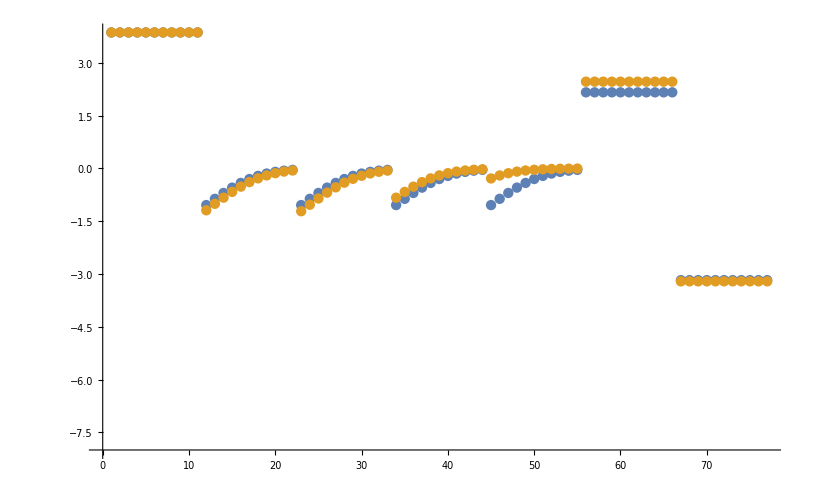

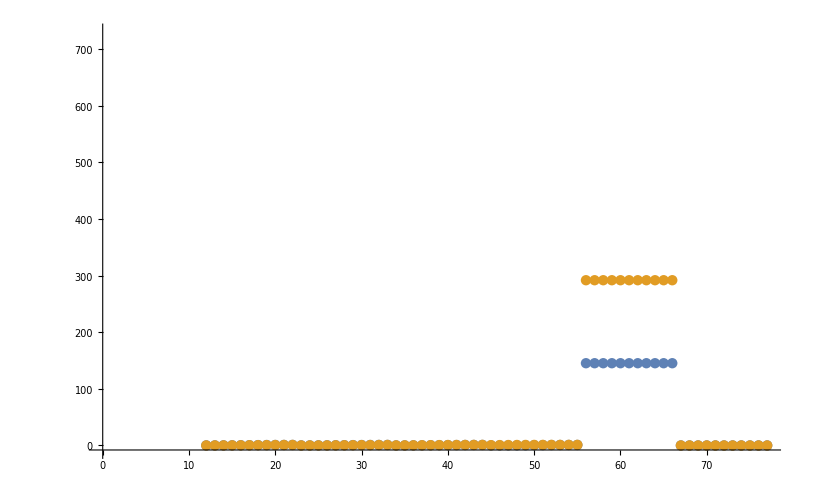

```mathematica
dataSetI=6;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

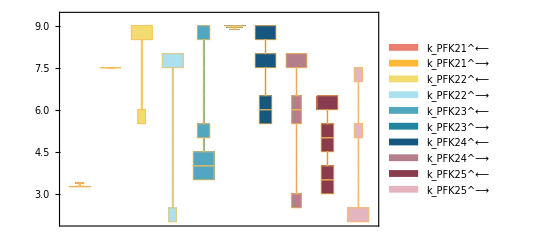

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;6,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

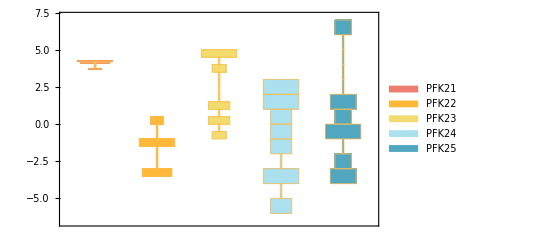

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

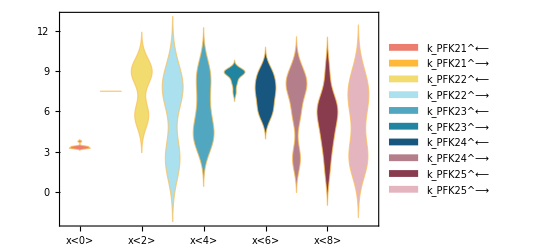

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

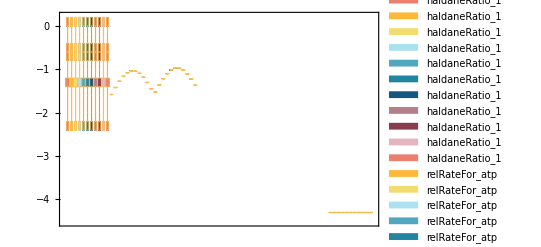

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

3.2587 | 7.49642 | 8.99942 | 7.60766 | 4.05331 | 9. | 7.7506 | 6.05106 | 4.71282 | 2.48333

#### Parameter Cluster Plots (Optional)

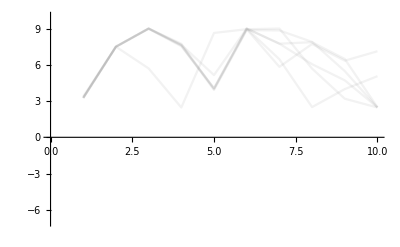

{-Graphics-}

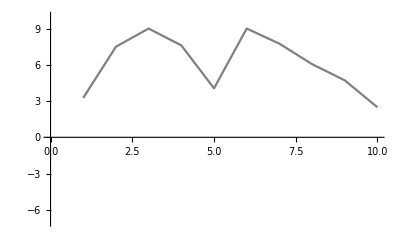

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
8.×10^-6 | 0.0000115938 | 44.9231
6.×10^-6 | 9.28272×10^-6 | 54.7121
0.00002 | 0.0000115938 | 42.0308
0.0001 | 9.28272×10^-6 | 90.7173

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
145.214 | 290.886 | 100.315

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
7304.8 | 7304.79 | 0.0000734297

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
7304.8 | 7304.79 | 0.0000734297

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

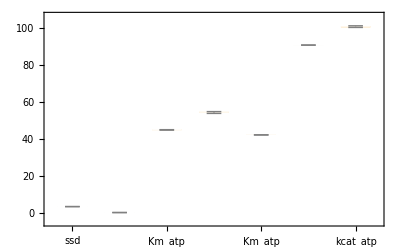

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 5;
```

/Users/guest/Desktop/internship stuff/MASSef/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/pfk2 already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/pfk2\rateconst_labels_pfk2.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/pfk2\S_pfk2.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PFK2[c],E_PFK2[c]&f6p,E_PFK2[c]&fdp,E_PFK2[c]&f6p&atp,adp[c],atp[c],f6p[c],fdp[c],E_PFK2[c]&fdp&adp}

/Users/guest/Desktop/internship stuff/MASSef/pfk2\species_pfk2.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PFK21: E_PFK2[c] + f6p[c] <=> E_PFK2[c]&f6p,PFK22: E_PFK2[c]&fdp <=> E_PFK2[c] + fdp[c],PFK23: atp[c] + E_PFK2[c]&f6p <=> E_PFK2[c]&f6p&atp,PFK24: E_PFK2[c]&fdp&adp <=> adp[c] + E_PFK2[c]&fdp,PFK25: E_PFK2[c]&f6p&atp <=> E_PFK2[c]&fdp&adp}

/Users/guest/Desktop/internship stuff/MASSef/pfk2\reactions_pfk2.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship\ stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PFK2[c],E_PFK2[c]&f6p,E_PFK2[c]&fdp,E_PFK2[c]&f6p&atp,E_PFK2[c]&fdp&adp}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK24_fwd*param_PFK2_total) - k_PFK21_rev*k_PFK22_fwd*k_PFK24_fwd*k_PFK25_fwd*param_PFK2_total - atp(c)*k_PFK22_fwd*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd*param_PFK2_total - k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK25_rev*param_PFK2_total - adp(c)*k_PFK21_rev*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev*param_PFK2_total)/(atp(c)*f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_fwd*k_PFK24_fwd + f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_rev*k_PFK24_fwd + k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK24_fwd + fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK23_rev*k_PFK24_fwd + adp(c)*fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK23_rev*k_PFK24_rev + atp(c)*f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_fwd*k_PFK25_fwd + f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK24_fwd*k_PFK25_fwd + k_PFK21_rev*k_PFK22_fwd*k_PFK24_fwd*k_PFK25_fwd + fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK24_fwd*k_PFK25_fwd + atp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd + atp(c)*k_PFK22_fwd*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd + atp(c)*fdp(c)*k_PFK22_rev*k_PFK23_fwd*k_PFK24_fwd*k_PFK25_fwd + adp(c)*fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK24_rev*k_PFK25_fwd + adp(c)*atp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_fwd*k_PFK24_rev*k_PFK25_fwd + adp(c)*atp(c)*fdp(c)*k_PFK22_rev*k_PFK23_fwd*k_PFK24_rev*k_PFK25_fwd + atp(c)*f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_fwd*k_PFK25_rev + f6p(c)*k_PFK21_fwd*k_PFK22_fwd*k_PFK23_rev*k_PFK25_rev + k_PFK21_rev*k_PFK22_fwd*k_PFK23_rev*k_PFK25_rev + fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK23_rev*k_PFK25_rev + adp(c)*fdp(c)*k_PFK21_rev*k_PFK22_rev*k_PFK24_rev*k_PFK25_rev + adp(c)*atp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_fwd*k_PFK24_rev*k_PFK25_rev + adp(c)*atp(c)*fdp(c)*k_PFK22_rev*k_PFK23_fwd*k_PFK24_rev*k_PFK25_rev + adp(c)*f6p(c)*k_PFK21_fwd*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev + adp(c)*k_PFK21_rev*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev + adp(c)*fdp(c)*k_PFK22_rev*k_PFK23_rev*k_PFK24_rev*k_PFK25_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/pfk2\rateconst_clusters_pfk2.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/pfk2\rateLaw_pfk2.txt